```mathematica
M32x32= Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\CriticalExponents\\Metropolis\\32x32\\experiment.txt","Table"];
```

```mathematica
WL32x32= Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\CriticalExponents\\Wanglandau\\32x32\\experiment.txt","Table"];
```

```mathematica
M128x128= Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\CriticalExponents\\Metropolis\\128x128\\experiment.txt","Table"];
```

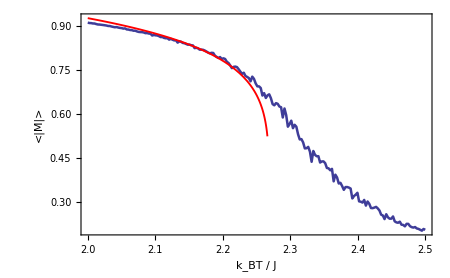

```mathematica
h1=criticalPlot[M32x32,1.21]
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\critexp32-metropolis.eps", h1];
```

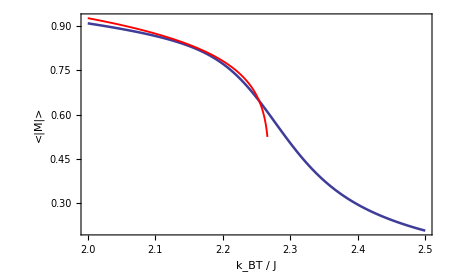

```mathematica
h2=criticalPlot[WL32x32,1.21]
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\critexp32-wanglandau.eps", h2];
```

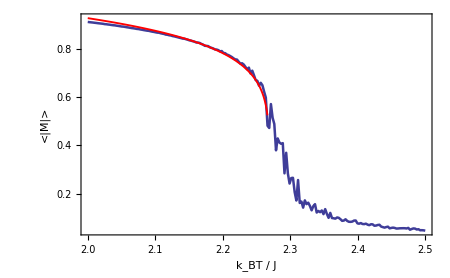

```mathematica
h3 = criticalPlot[M128x128,1.21]
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\critexp128-metropolis.eps", h3];
```